```mathematica
gapmax=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e3-e6-e7-2e2-max.txt",{Number,Number}];
check3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/analytical.d0.02-check3.txt",{Number,Number}];
gap8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e6-e6-e6-5e2.txt",{Number,Number}];
```

```mathematica
Function[{u},a-b*Exp[-u/(p/α+0.5)]][3]
```

```mathematica
ClearAll[a,b,p,α]
m=11;
pg1[m-1]=α;
pg1[m]=(1-3p-α(1-4p))α+Function[{u},a-b*Exp[-u/(p/α+0.5)]][m];
pg1[m+1]=p(1-α)α+Function[{u},a-b*Exp[-u/(p/α+0.5)]][m+1];
For [i=m+2,i<501,i++,
pg1[i]=Function[{u},a-b*Exp[-u/(p/α+0.5)]][i];
]
```

```mathematica
d=0.02;
a=0;
α=p/(1/d-m-0.5);
p=0.09;
```

```mathematica
Solve[Sum[pg1[x],{x,m-1,500}]==1,b]
```

{{b→-0.0334214}}

```mathematica
b=-0.03342137535311648;
```

```mathematica
data1=Table[{i+1,pg1[i]},{i,m-1,300}];
```

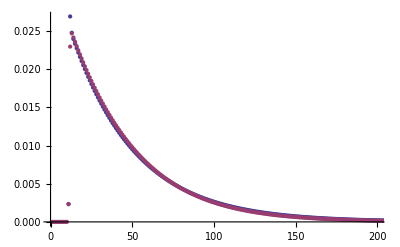

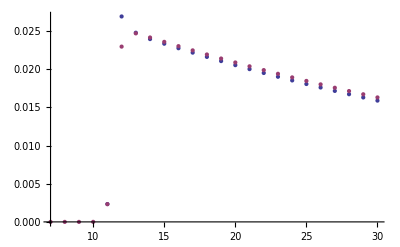

```mathematica
ListPlot[{data1,check3},PlotRange->{{0,200},Full}]
ListPlot[{data1,check3},PlotRange->{{7,30},Full}]
```

```mathematica
-------------------
```

```mathematica
ClearAll[a,b,p,α]
m=11;

For [i=m+2,i<501,i++,
pg2[i]=Function[{u},a-b*Exp[-u/(p/α+0.5)]][i];
]

pg2[m-1]=α;
pg2[m]=((1-2p-α(1-3p))α+(p+α(1-3p))pg2[m+1]+α*p*pg2[m+2])/(2p+α(1-3p));
pg2[m+1]=p(1-α)α+Function[{u},a-b*Exp[-u/(p/α+0.5)]][m+1];
```

```mathematica
a=0;
d=0.02;
α=p/(1/d-m-0.5);
p=0.09;
```

```mathematica
Solve[Sum[pg2[x],{x,m-1,500}]==1,b]
```

{{b→-0.0335523}}

```mathematica
b=-0.03355225757532773;
```

```mathematica
data2=Table[{i+1,pg2[i]},{i,m-1,300}];
```

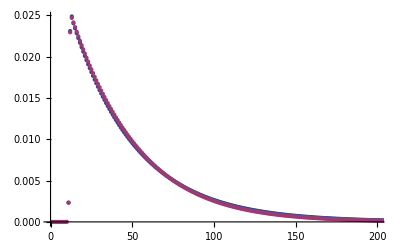

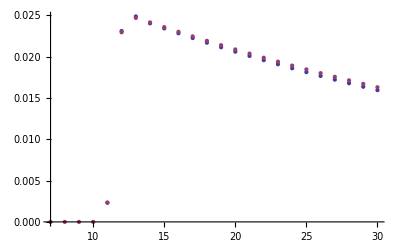

```mathematica
ListPlot[{data2,check3},PlotRange->{{0,200},Full}]
ListPlot[{data2,check3},PlotRange->{{7,30},Full}]
```

```mathematica
ClearAll[a,b,p,α]
m=11;

For [i=m+2,i<501,i++,
pg3[i]=Function[{u},a-b*Exp[-u/(p/α+0.5)]][i];
]

pg3[m-1]=α;
a=0;
d=0.02;
α=p/(1/d-m-0.5);
p=0.09;
ClearAll[pg3[m],pg3[m+1]]
Solve[{x-((1-2p-α(1-3p))α+(p+α(1-3p))y+α*p*pg3[m+2])/(2p+α(1-3p))==0,
y-(p(1-α)α+p(1-α)x+(p+α(1-3p))pg3[m+2])/(2p+α(1-3p))==0},{x,y}]
```

{{x→0.0148019-0.24426 b,y→0.00846944-0.48233 b}}

```mathematica
pg3[m]=0.01480187368343307-0.24425971904967309 b;
pg3[m+1]=0.008469440094818918-0.4823303630838504 b;
```

```mathematica
Solve[Sum[pg3[x],{x,m-1,500}]==1,b]
```

{{b→-0.0335638}}

```mathematica
b=-0.03356380759099609;
```

```mathematica
data3=Table[{i+1,pg3[i]},{i,m-1,300}];
```

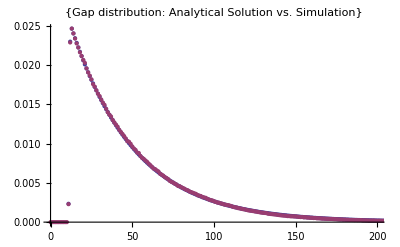

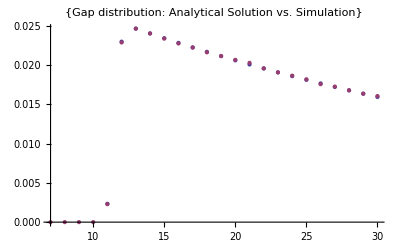

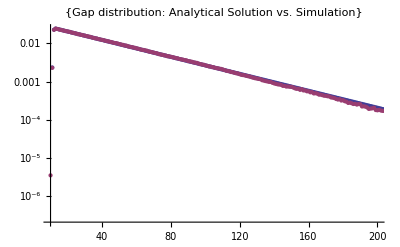

```mathematica
ListPlot[{data3,gapmax},PlotRange->{{0,200},Full},PlotLabel->{"Gap distribution: Analytical Solution vs. Simulation"}]
ListPlot[{data3,gapmax},PlotRange->{{7,30},Full},PlotLabel->{"Gap distribution: Analytical Solution vs. Simulation"}]
ListLogPlot[{data3,gapmax},PlotRange->{{10,200},Full},PlotLabel->{"Gap distribution: Analytical Solution vs. Simulation"}]
```

```mathematica
d=0.02;
m=11.;
p/(1/d-m-0.5)
```

0.00233766

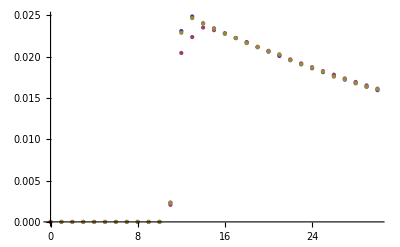

```mathematica
ListPlot[{data2,gap8,gapmax},PlotRange->{{0,30},Full}]
```